### Функции плотности вероятности различных распределений

```mathematica
data1=RandomVariate[NormalDistribution[],100000];
```

```mathematica
RandNormal[count_, center_]:=RandomVariate[NormalDistribution[center, 3], count];
```

#### Математическое ожидание

```mathematica
Mean[data1]
```

```mathematica
0.0000001
```

```mathematica
{0,1,0,1,0,1}
```

#### Нормальное распределение

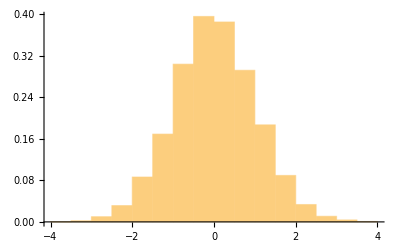

```mathematica
Show[Histogram[data1,Automatic,"ProbabilityDensity"]]
```

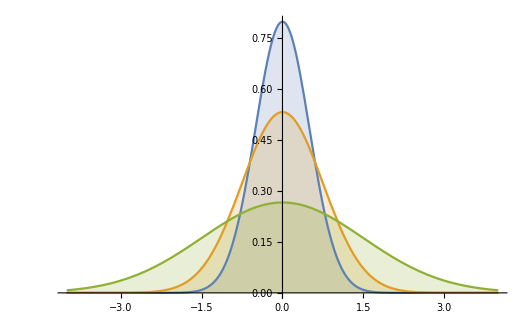

```mathematica
Plot[Table[PDF[NormalDistribution[0,σ],x],{σ,{0.5,0.75,1.5}}]//Evaluate,{x,-4,4},Filling->Axis]
```

#### Логнормальное распределение

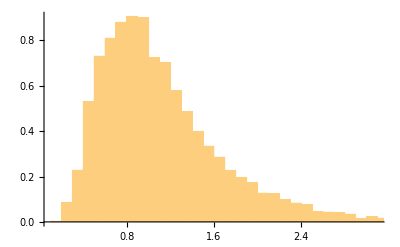

```mathematica
data2 = RandomVariate[LogNormalDistribution[0,0.5], 10000];
Show[Histogram[data2,Automatic,"ProbabilityDensity"]]
```

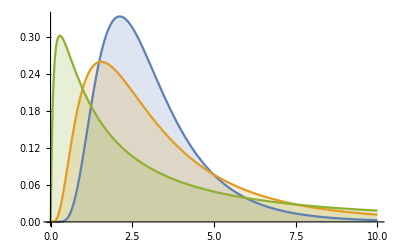

```mathematica
Plot[Table[PDF[LogNormalDistribution[1,σ],x],{σ,{0.5,0.75,1.5}}]//Evaluate,{x,0,10},Filling->Axis, PlotRange->All]
```

#### Распределение Пуассона

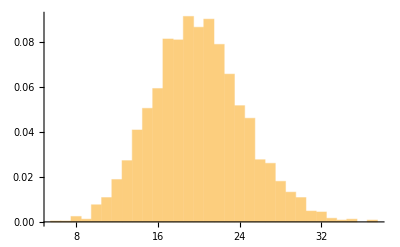

```mathematica
data3=RandomVariate[PoissonDistribution[20],2500];
Show[Histogram[data3,Automatic,"ProbabilityDensity"]]
```

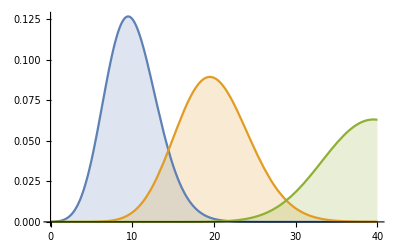

```mathematica
Plot[Table[PDF[PoissonDistribution[mu],x],{mu,{10,20,40}}]//Evaluate,{x,0,40},Filling->Axis]
```

#### Функция плотности и доверительный интервал

```mathematica
pdfNormal=PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
{xl,xr}=Function[α,Quantile[NormalDistribution[],{(1-α)/2.0,(1+α)/2.0}]][Quantity[95, "Percent"]]
```

{-1.95996,1.95996}

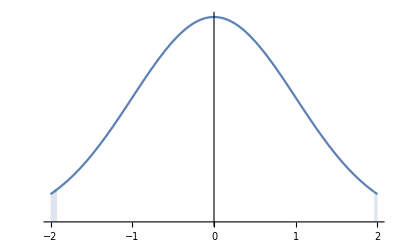

```mathematica
Show[Plot[pdfNormal,{x,-2,2},Filling->Axis,AxesOrigin->{0,0},RegionFunction->(Not[xl<#<xr]&)],Plot[pdf,{x,xl,xr}],PlotRange->{0,0.4},Ticks->{Automatic,None}]
```

### Тестирование ПСЧ методом проверки статистической гипотезы

```mathematica
h1=DistributionFitTest[data1,Automatic,"HypothesisTestData"];
h2=DistributionFitTest[data2,Automatic,"HypothesisTestData"];
```

```mathematica
h1["TestDataTable", All]
```

| Statistic | P-Value
Anderson-Darling | 0.757408 | 0.0475164
Baringhaus-Henze | 1.28315 | 0.062926
Cramér-von Mises | 0.13739 | 0.0343055
Jarque-Bera ALM | 5.68637 | 0.061046
Kolmogorov-Smirnov | 0.00752771 | 0.19819
Kuiper | 0.0147229 | 0.0562544
Mardia Combined | 5.68637 | 0.061046
Mardia Kurtosis | 2.05583 | 0.0397993
Mardia Skewness | 1.40219 | 0.236358
Pearson χ^2 | 71.088 | 0.668243
Watson U^2 | 0.130177 | 0.0318065

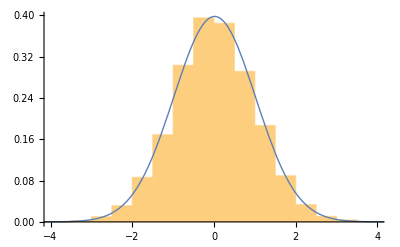

```mathematica
Show[Histogram[data1,Automatic,"ProbabilityDensity"],Plot[PDF[h1["FittedDistribution"],x],{x,-5,5},PlotStyle->Thick]]
```

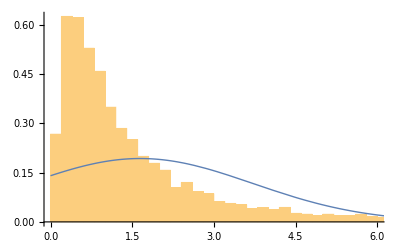

```mathematica
Show[Histogram[data2,Automatic,"ProbabilityDensity"],Plot[PDF[h2["FittedDistribution"],x],{x,0,20},PlotStyle->Thick]]
```